# Synchrotron Bending Magnet Radiation

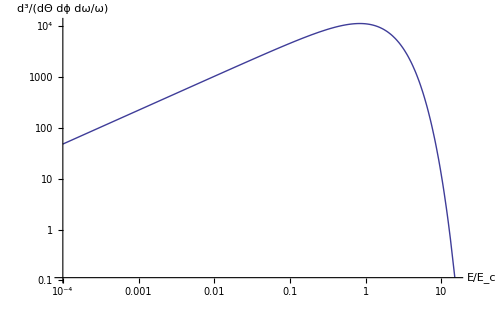

```mathematica
plot=LogLogPlot[1.33*10^4*(1.7)^2*200*10^-3 x^2 BesselK[2/3,x/2]^2,{x,0.0001,15}, AxesLabel->{Style["E/E_c",14],Style["d^3/(dΘ dϕ dω/ω)",14],}, ImageSize->500]
```

```mathematica
Assuming[x>0,{G1[x_]=x*∫_x^∞ BesselK[5/3,y]ⅆy}]
```

{x (1/x^(2/3)2^(2/3) Gamma[2/3] HypergeometricPFQ[{-1/3},{-2/3,2/3},x^2/4]+(π (-320+(81 2^(1/3) x^(8/3) HypergeometricPFQ[{4/3},{7/3,8/3},x^2/4])/Gamma[-1/3]))/(320 √3))}

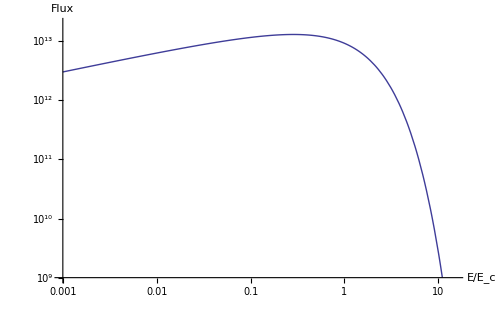

```mathematica
plot2=LogLogPlot[2.46*10^13*(1.7)^2*200*10^-3*G1[x],{x,0.001,15},PlotRange->{10^9,2*10^13}, AxesLabel->{Style["E/E_c",14],Style["Flux",14]}, ImageSize->500]
```

Flux is in (photons/s)/(0.1% BW)

```mathematica
Export["flux.png", 
  plot2, "PNG"]
```

flux.png